```mathematica
Needs["Splines`"]
```

```mathematica
SetDirectory["/users/tp/julian/mathematica/electron"]
```

/users/tp/julian/mathematica/electron

```mathematica
Directory[]
```

/users/tp/julian/mathematica/electron

```mathematica
epcg[xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid,curve},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};


e[u_]:=initialcurve[u];

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ListPlot[Table[spline[2+(n)i/100],{i,0,100}]],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ParametricPlot[spline[u],{u,2,2+n}]],
Show[
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}]],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ParametricPlot[initialcurve[u],{u,0,2Pi}]]
}}]
];
]
```

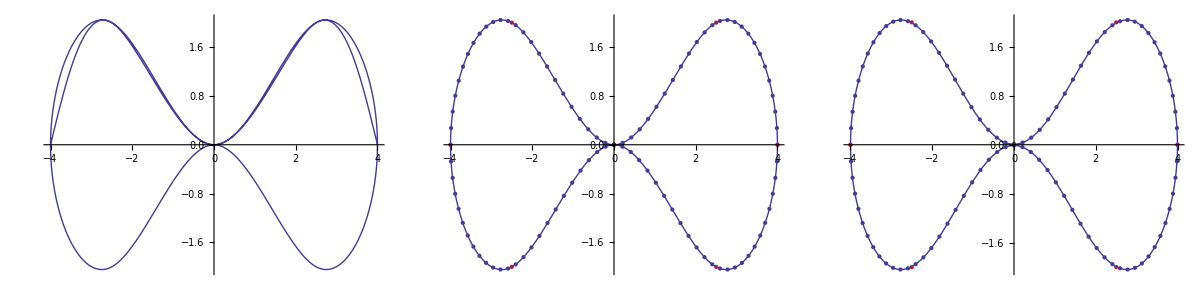

```mathematica
Block[{h=2,t=2.5,w=4},
epcg[{{0,0},{t,h},{w,0},{t,-h},{0,0},{-t,-h},{-w,0},{-t,h}}]]
```

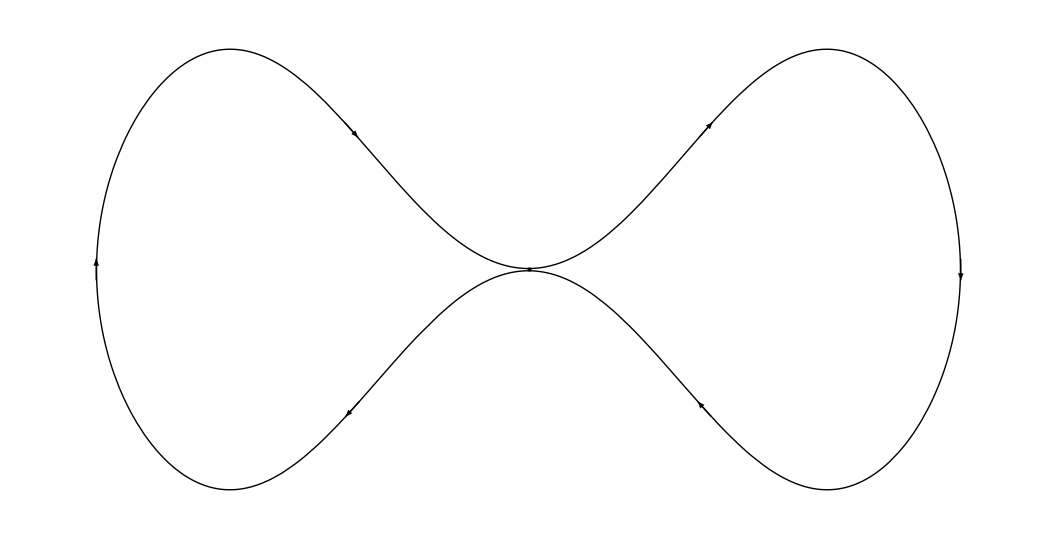

```mathematica
Block[{thick=.025,w=4},
eplot=ParametricPlot[e[u],{u,0,2π},Axes->False,PlotStyle->{Black},PlotRange->Full,
Epilog->{
{Black,PointSize[Medium],Point[{0,0}]},
{Arrowheads[thick],Arrow[{{w,0.1},{w,-0.1}}]},
{Arrowheads[thick],Arrow[{e[π/6.5],e[π/6]}]},
{Arrowheads[thick],Arrow[{{-w,-0.1},{-w,0.1}}]},
{Arrowheads[thick],Arrow[{e[π/6.5+π],e[π/6+π]}]},
{Arrowheads[thick],Arrow[{e[-π/6],e[-π/6.5]}]},
{Arrowheads[thick],Arrow[{e[-π/6-π],e[-π/6.5-π]}]}
}]
]
```

```mathematica
Export["plot.electron.eps",eplot]
```

plot.electron.eps